```mathematica
denom[a_,b_,xlower_,xupper_,ylower_,yupper_]:=NIntegrate[1/(1+(a - x)^2 + b(y - x^2)^2),{x,xlower,xupper},{y,ylower, yupper},AccuracyGoal->Infinity,MaxRecursion->100000,MaxPoints->10000000]
```

```mathematica
denom[1,100,-2,4,-1,12]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.05461

```mathematica
NumberForm[1.0546134367037538,16]
```

1.054613436703754

```mathematica
NumberForm[1.0546134367037538,16]
```

1.054613436703754

```mathematica
fUnnormalisedRosenbrock[x_,y_,a_,b_]:=((a - x)^2 + b(y - x^2)^2)
```

```mathematica
fUnnormalisedRosenbrock[10, 10, 1, 100]
```

810081

```mathematica
fUnnormalisedRosenbrockLogPDF[x_,y_,a_,b_]:=Log[1 / (1+((a - x)^2 + b(y - x^2)^2))]
```

```mathematica
fUnnormalisedRosenbrockLogPDF[1, 1, 1,100]
```

0

```mathematica
N@D[fUnnormalisedRosenbrockLogPDF[x, y, 1, 100],x]/.{x->3, y->4}
```

-2.39681

```mathematica
fUnnormalisedRosenbrockLogPDF[0.5,6,1,100]
```

-8.10395

```mathematica
(1 + fUnnormalisedRosenbrock[0.5,6,1,100])
```

3307.5

```mathematica
NumberForm[0.0003023431594860166,16]
```

0.0003023431594860166

```mathematica
N[-Log[810082]]
```

-13.6049

```mathematica
fRosenbrockPDF[x_,y_,a_,b_,xlower_,xupper_,ylower_,yupper_]:=1/(1+(a - x)^2 + b(y - x^2)^2) / denom[a,b,xlower,xupper,ylower,yupper]
```

```mathematica
NIntegrate[(x-0.87)(y- 2.6)fRosenbrockPDF[x,y,1,100,-2,4,-1,12],{x,-2,4},{y,-1,12},AccuracyGoal->Infinity]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

2.70258

```mathematica
NIntegrate[(y-2.60)^2 fRosenbrockPDF[x,y,1,100,-2,4,-1,12],{x,-2,4},{y,-1,12},AccuracyGoal->Infinity]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

8.52658

```mathematica
D[Log[1/(1+(a - x)^2 + b(y - x^2)^2) ],x]
```

-(-2 (a-x)-4 b x (-x^2+y))/(1+(a-x)^2+b (-x^2+y)^2)

```mathematica
D[Log[1/(1+(a - x)^2 + b(y - x^2)^2) ],y]
```

-(2 b (-x^2+y))/(1+(a-x)^2+b (-x^2+y)^2)

```mathematica
1/(1.0546134367037538(1+(1 - x)^2 + 100(y - x^2)^2))
```

```mathematica
ContourPlot[fRosenbrockPDF[x,y,1,100],{x,-2,4},{y,-1,12},Contours->200,PlotRange->Full,PlotPoints->100]
```

-Graphics-

```mathematica
D[RealAbs[x],x]/.{x->0}
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
Norm[{x,y}]
```

```mathematica
D[(√(x^2+y^2+z^2))^β,x]
```

x (x^2+y^2+z^2)^(-1+β/2) β

```mathematica
fConeLogDeriv[x__,β_]:=Block[{cons=β(Norm[x]^2)^(-1 + β /2)},Table[cons * x[[i]],{i,1,Length@x,1}]]
```

```mathematica
N@fConeLogDeriv[{-1,3},1]
```

{-0.316228,0.948683}

```mathematica
N@fConeLogDeriv[{-1,3,2,4,5,6,7,8,9,10},0.3]
```

{-0.00190318,0.00570954,0.00380636,0.00761272,0.00951589,0.0114191,0.0133223,0.0152254,0.0171286,0.0190318}

```mathematica
N@Abs'[1]
```

Abs'[1.]

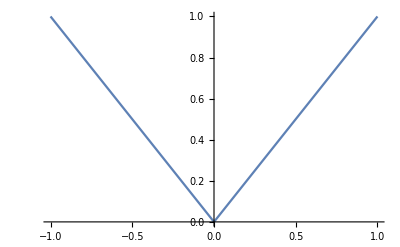

```mathematica
Plot[Abs[x],{x,-1,1}]
```

```mathematica
D[Abs'[x], x]
```

Abs''[x]